```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/6 семестр/6.1/6.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/6 семестр/6.1/~$6.1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/6 семестр/6.1/6.1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

## Спектр

```mathematica
dataset1=raw⟦6⟧⟦4;;⟧
```

{{1.,498.4},{1.5,349.9},{2.,558.5},{2.5,1068.1},{3.,1583.1},{3.5,1950.3},{4.,2258.},{4.5,2652.8},{5.,3281.8},{5.5,3906.7},{6.,4423.1},{6.5,4382.2},{7.,3671.7},{7.5,2757.9},{8.,1716.4},{8.5,964.},{9.,475.8},{9.5,259.7}}

```mathematica
exp = NonlinearModelFit[dataset1⟦12;;⟧,A Exp[B/T],{A,B},T]
```

FittedModel[14.0509 ⅇ^(37.896/T)]

```mathematica
(*maxX=Max[dataset1⟦All,1⟧]*)
```

```mathematica
(*minX=Min[dataset1⟦All,1⟧]*)
```

```mathematica
(*maxY=Max[dataset1⟦All,2⟧]*)
```

```mathematica
(*minY=Min[dataset1⟦All,2⟧]*)
```

```mathematica
(*lengthX=maxX-minX;
lengthY=maxY-minY;*)
```

```mathematica
(*DeltaX = Round[lengthX*0.1;*)
```

```mathematica
(*DeltaY = lengthY*0.1;*)
```

```mathematica
(*leftX=Round[minX-DeltaX]*)
```

```mathematica
(*rightX=Round[maxX+DeltaX]*)
```

```mathematica
exp = NonlinearModelFit[dataset1,(A Exp[(-(U-U0)^2)/(2 σ^2)])/(√(2π) σ),{A,U0,σ},U]
```

FittedModel[4181.04 ⅇ^(-0.163013 (-5.83894+U)^2)]

```mathematica
exp["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 18354.7 | 772.762 | 23.7521 | 2.57845×10^-13
U0 | 5.83894 | 0.0845427 | 69.065 | 3.3795×10^-20
σ | 1.75136 | 0.0863202 | 20.2891 | 2.56263×10^-12

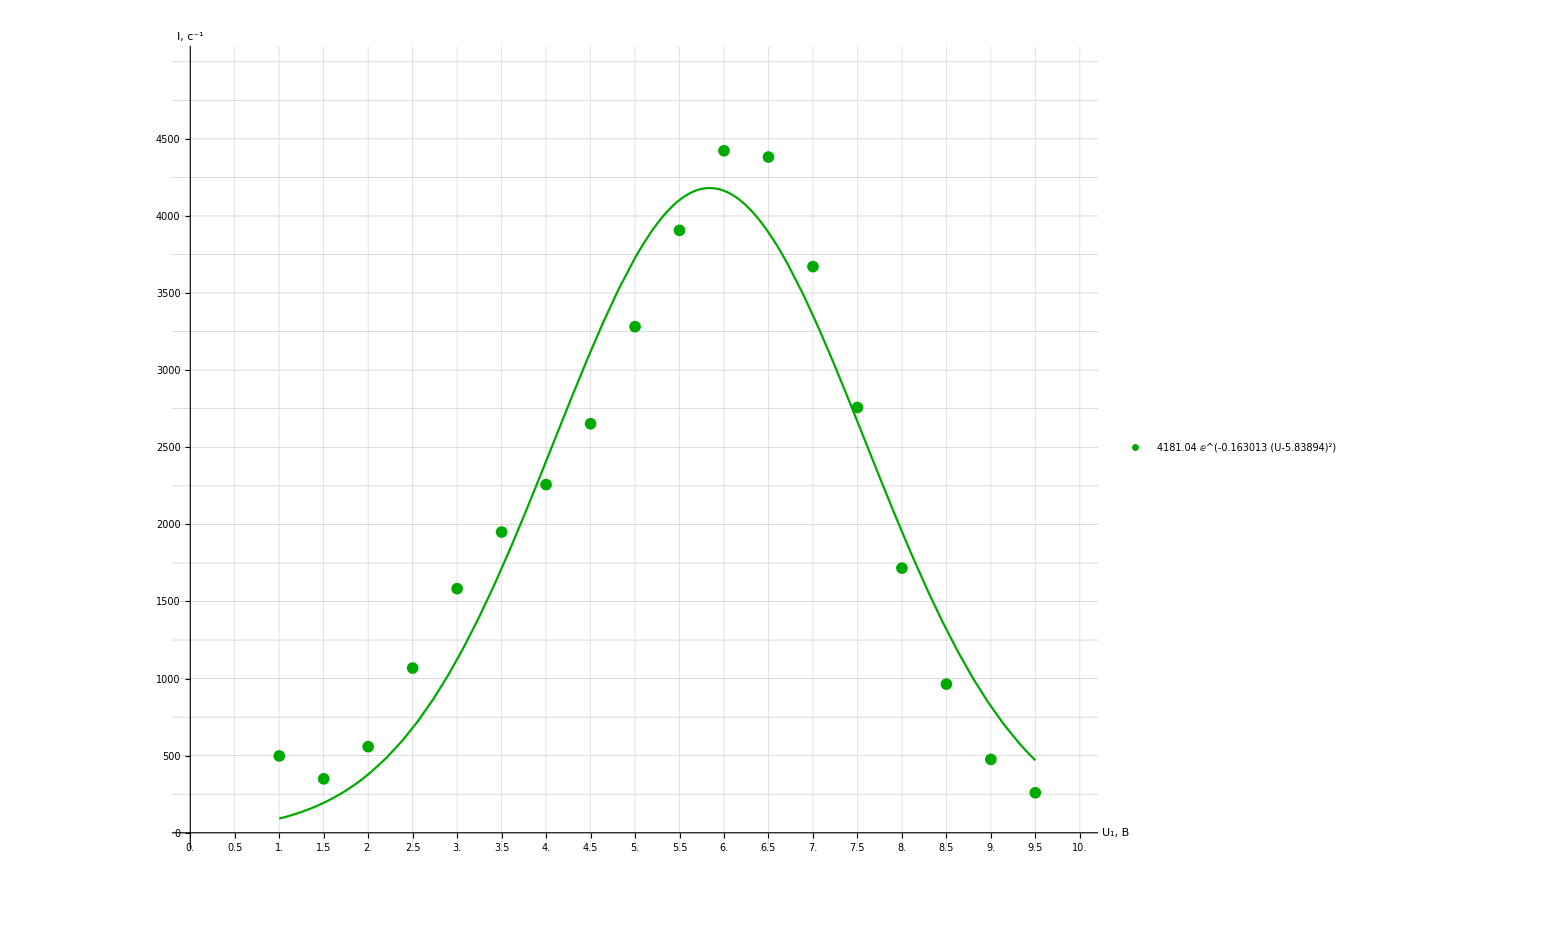

```mathematica
Show[
ListPlot[
{dataset1},
PlotRange-> {{0,10},{0,5000}},
Ticks-> {Range[0,maxX+DeltaX, 0.5],Range[0,maxY+DeltaY, 500]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["U_1, В", Large], Style["I, (:0441)^-1", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.25],Range[-1000,6000, 250]},
LabelStyle->Black,
PlotStyle->Darker@Green,
(*Joined->True,
InterpolationOrder->3,*)
PlotLegends->Placed[LineLegend[
{Normal@exp},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[{exp[x]},{x,1,9.5},
PlotStyle->Darker@Green
]
]
```

```mathematica
Solve[D[Normal[exp],U]==0,U]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{U→5.83894}}

## Скорость

```mathematica
data1= raw⟦7⟧⟦2;;⟧
```

{{-6.98,36734.5},{-6.28,36727.9},{-5.14,36723.6},{-4.76,36741.8},{-3.99,36723.},{-3.75,36712.9},{-3.66,37109.1},{-3.47,36755.1},{-2.87,37097.4},{-2.57,37040.8},{-2.41,37024.1},{-2.02,36766.2},{-1.58,37119.2},{-1.14,36731.},{-0.9,37100.3},{0.7,37572.3},{0.91,37238.3},{1.25,37410.6},{1.6,36617.3},{1.92,36100.5},{2.06,35460.3},{2.26,34412.4},{2.74,34547.9},{2.9,35678.3},{2.96,35534.1},{3.16,36317.8},{3.72,36867.8},{4.04,37111.6},{4.9,37357.4},{5.52,37410.8}}

```mathematica
data2= raw⟦8⟧⟦2;;⟧
```

{{-6.3,16299.7},{-5.17,16324.5},{-4.85,16309.8},{-4.31,16267.9},{-4.01,16255.7},{-3.89,16256.5},{-3.83,16286.5},{-3.65,16196.1},{-3.2,16166.5},{-2.9,16228.2},{-2.77,16187.7},{-2.58,16174.1},{-2.44,16194.3},{-2.01,16222.1},{-1.99,16186.2},{-1.59,16211.2},{-1.13,16267.7},{0.88,16314.1},{1.26,16098.1},{1.56,15755.1},{1.62,15718.1},{1.95,14787.9},{2.03,14458.8},{2.21,13810.9},{2.31,13534.8},{2.55,13488.4},{2.89,14508.8},{3.,14845.7},{3.07,15114.6},{3.16,15331.1},{3.39,15697.8},{3.79,16035.4},{4.07,16143.4},{4.95,16328.7}}

```mathematica
data3=raw⟦9⟧⟦2;;⟧
```

{{-7.25,4400.3},{-7.03,4407.3},{-6.27,4538.},{-5.15,4557.1},{-4.31,4534.4},{-3.79,4557.4},{-3.47,4572.3},{-3.2,4550.8},{-3.12,4563.3},{-3.04,4539.6},{-2.83,4546.7},{-2.48,4526.1},{-2.02,4538.7},{-2.01,4512.9},{-1.93,4521.},{-1.49,4537.8},{-1.17,4366.7},{-1.07,4350.1},{0.85,4249.},{0.94,4269.8},{1.17,4347.8},{1.52,4191.},{1.6,4137.5},{1.61,4158.7},{1.98,3757.1},{2.22,3460.9},{2.4,3383.5},{2.43,3384.2},{2.55,3376.3},{2.73,3531.5},{2.98,3816.2},{3.38,4143.9},{4.05,4371.5},{4.93,4461.4},{5.54,4358.4},{5.7,4347.6}}

```mathematica
data4=raw⟦10⟧⟦2;;⟧
```

{{-7.26,42649.4},{-7.06,42656.4},{-6.87,42631.5},{-6.64,42670.3},{-6.39,42515.1},{-6.37,42556.5},{-5.62,41459.1},{-3.72,41099.1},{-2.53,40308.2},{-2.01,39591.9},{-1.94,39358.9},{-1.57,38272.1},{-1.57,38221.4},{-1.55,38168.9},{-1.29,36907.8},{-1.22,36451.6},{-1.1,36001.3},{-0.87,34248.8},{0.7,35443.4},{0.87,36986.1},{1.02,37905.3},{1.25,39187.7},{1.29,37663.7},{1.53,39230.5},{1.54,39226.7},{1.59,40357.6},{1.91,40181.},{2.82,41114.7},{2.92,41795.},{4.39,42260.9},{4.99,43129.},{5.,43059.5},{5.2,43135.5},{5.4,43190.8},{5.58,43127.1},{5.75,43166.1}}

```mathematica
noline1=NonlinearModelFit[data1(*⟦16;;⟧*),a+b 1/(1+((v-v0)/(Γ/2))^2),{{a,900},{b,100},{v0,2.1},{Γ,0.4}},v]
```

FittedModel[37038.8-4386.31/(1+11.9166 (-2.49137+v)^2)]

```mathematica
Magnify[noline1["ParameterTable"],2]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 37038.8 | 66.7893 | 554.562 | 1.74486×10^-54
b | -4386.31 | 1000.34 | -4.3848 | 0.000170433
v0 | 2.49137 | 0.0198736 | 125.361 | 1.05619×10^-37
Γ | -0.579366 | 0.130298 | -4.44648 | 0.000144866

```mathematica
noline1[2.49137]
```

32652.5

```mathematica
noline2=NonlinearModelFit[data2,a+b 1/(1+((v-v0)/(Γ/2))^2),{{a,100},{b,100},{v0,2.49},{Γ,0.4}},v]
```

FittedModel[16305.3-3056.55/(1+4.32812 (-2.4573+v)^2)]

```mathematica
Magnify[noline2["ParameterTable"],2]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 16305.3 | 24.8223 | 656.881 | 6.18786×10^-64
b | -3056.55 | 84.7486 | -36.0661 | 2.88208×10^-26
v0 | 2.4573 | 0.0115986 | 211.862 | 3.39451×10^-49
Γ | -0.961347 | 0.0394428 | -24.3732 | 2.50195×10^-21

```mathematica
noline2[2.4573]
```

13248.7

```mathematica
noline3=NonlinearModelFit[data3,a+b 1/(1+((v-v0)/(Γ/2))^2),{{a,100},{b,100},{v0,2.4},{Γ,0.4}},v]
```

FittedModel[4511.06-1153.14/(1+2.50551 (-2.46217+v)^2)]

```mathematica
Magnify[noline3["ParameterTable"],2]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 4511.06 | 15.2929 | 294.978 | 1.55817×10^-56
b | -1153.14 | 35.9751 | -32.0537 | 6.81401×10^-26
v0 | 2.46217 | 0.0260273 | 94.5995 | 9.45922×10^-41
Γ | -1.26352 | 0.0798778 | -15.8181 | 1.1057×10^-16

```mathematica
noline3[2.46217]
```

3357.93

```mathematica
noline4=NonlinearModelFit[data4,a+b 1/(1+((v-v0)/(Γ/2))^2),{{a,300},{b,300},{v0,-0.1},{Γ,1.8}},v]
```

FittedModel[43128.5-11331.8/(1+0.681666 (0.206038+v)^2)]

```mathematica
Magnify[noline4["ParameterTable"],2]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 43128.5 | 149.503 | 288.48 | 3.17739×10^-56
b | -11331.8 | 779.547 | -14.5364 | 1.19839×10^-15
v0 | -0.206038 | 0.0267407 | -7.70503 | 8.76367×10^-9
Γ | -2.42239 | 0.201062 | -12.048 | 1.97351×10^-13

```mathematica
noline4[-0.206038]
```

31796.7

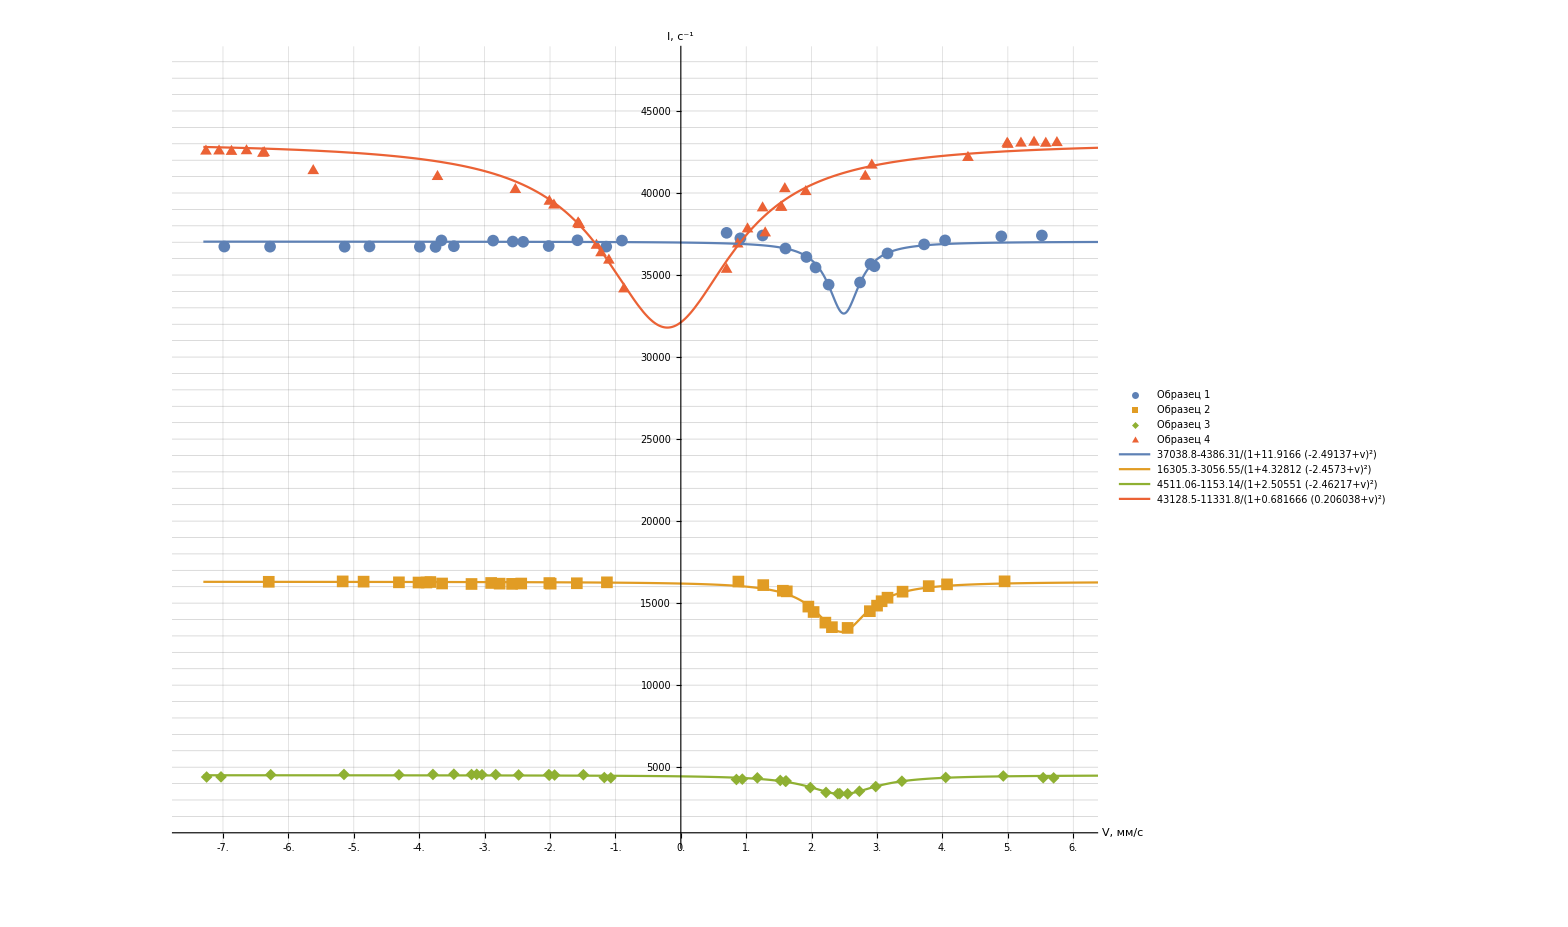

```mathematica
Show[
ListPlot[
{data1,data2,data3,data4},
PlotRange-> {{-7.5,6.1},{1000,48000}},
Ticks-> {Range[-10,10, 0.5],Range[0,60000, 5000]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["V, мм/с", Large], Style["I, (:0441)^-1", Large]},
AxesStyle->Directive[Arrowheads[0.01],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.25],Range[-1000,60000,1000]},
LabelStyle->Black,
(*Joined->True,
InterpolationOrder->3,*)
PlotLegends->Placed[LineLegend[
{"Образец 1","Образец 2","Образец 3","Образец 4"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.85],Scaled[0.5]}
]
],
Plot[{noline1[x],noline2[x],noline3[x],noline4[x]},{x,-7.3,7},
PlotLegends->Placed[LineLegend[
{Normal@noline1,Normal@noline2,Normal@noline3,Normal@noline4},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.25],Scaled[0.5]}
]
]
]
```

```mathematica
|
```

```mathematica
Ё
```

Ё